```mathematica
Signal=Import["/Users/nv/Downloads/dataStream_14695_738.txt","Table"];
Template=Import["/Users/nv/Downloads/signalTemplate14695-738.out","Table"];
h=-0.0619508
```

-0.0619508

```mathematica
sortedPairs=SortBy[Transpose[{Template, Signal}],First[Position[Template,1]]];
sorted1=sortedPairs[[All,1]];
sorted2=sortedPairs[[All,2]];
```

```mathematica
Length[Signal]
S1=Reverse[SortBy[Signal,First[Position[Template,1]]]];
S2=Reverse[sorted2];
S3=Round[S2];
S4=S3-Min[S3]+1;
```

24

```mathematica
Length[Template]
T1=Reverse[SortBy[Template,First[Position[Template,1]]]];
T2=h*Reverse[sorted1];
T3=Round[T2];
T4=T3-Min[S3]+1;
ordering=OrderingBy[Template,First[Position[Template,1]]];
Signal[[ordering]];
```

24

```mathematica
Finish=First[Position[sorted1,1]][[2]]
```

33

```mathematica
Start=Last[Position[sorted1,1]][[2]]
```

28

```mathematica
array1=RandomInteger[{1,5},{24,61}]; (*Array of tile values (5x5 grid)*)
array2=RandomInteger[{1,10},{24,61}]; (*Array of edge colors (5x5 grid)*)
spacing=0.16
```

0.16

```mathematica
g=Graphics[Table[(*Create a rectangle for each tile*)Style[Rectangle[{i-1+spacing,j-1+spacing},{i,j}],FaceForm[ColorData[97,"ColorList"][[S4[[i,j]]]]],(*Fill color based on array1*)EdgeForm[{Thickness[0.005],ColorData[97,"ColorList"][[T4[[i,j]]]]}]],(*Edge color based on array2*){i,1,24},{j,1,61} (*Iterate over the grid*)],PlotRange->{{0,24},{0,61}},AspectRatio->2.54];
```

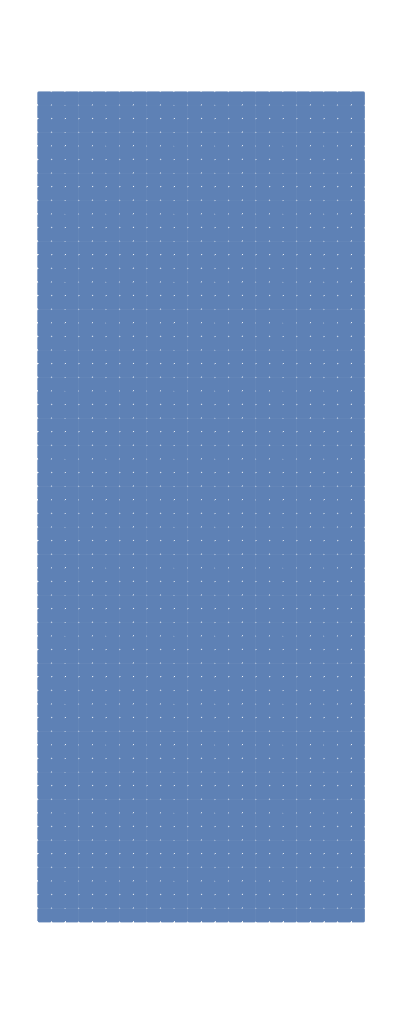

```mathematica
Rotate[g,1.5708]
```

```mathematica
RepresentArrays[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.005], Opacity[1],ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]}],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows},{0,cols}},AspectRatio->2.54]]
```

```mathematica
RepresentArrays2[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.002], Opacity[1],ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]}],FaceForm[{Opacity[0.01],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows},{0,cols}},AspectRatio->2.54]]
```

0.0619508

-0.0619508

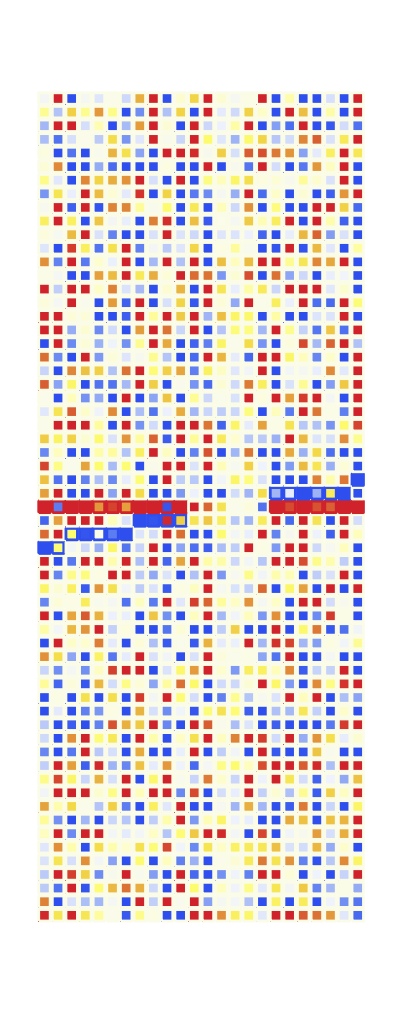

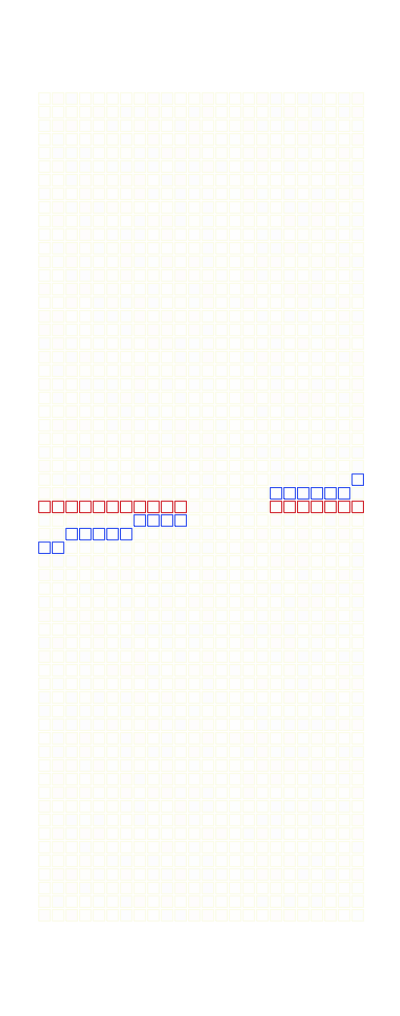

```mathematica
Max2=1.0*Max[Max[T2]]
Min2=1.0*Min[Min[T2]]
g2=RepresentArrays[T2,S2,Max2,Min2];
r2=Rotate[g2,-1.5708]
g3=RepresentArrays2[T2,S2,Max2,Min2];
r3=Rotate[g3,-1.5708]
```

```mathematica
RepresentArrays3[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.005],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[0.0],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows},{Start-1,Finish+1}},AspectRatio->(Finish-Start)/24]]
```

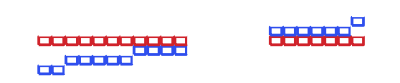

```mathematica
g4=RepresentArrays3[T2,S2,Max2,Min2];
r4=Rotate[g4,-1.5708]
```

```mathematica
o2=Overlay[{r2}]
```

-Graphics-

## Putting it together

```mathematica
spacing=0.4
```

0.4

```mathematica
BackFill[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.002], Opacity[1],White}],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
```

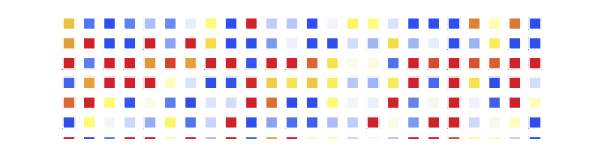

```mathematica
BF=BackFill[T2,S2,Max2,Min2];
bf=Rotate[BF,-1.5708]
```

```mathematica
FrontEdge[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.015],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[0],If[array2[[i,j]]>Max2,Black,ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]]}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
```

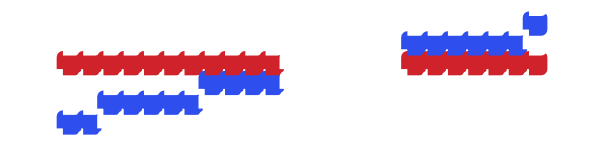

```mathematica
FE=FrontEdge[T2,S2,Max2,Min2];
fe=Rotate[FE,-1.5708]
```

```mathematica
Cutoff[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i-0.1,j-0.1},{i-1+spacing+0.1,j-1+spacing+0.1}],EdgeForm[{Thickness[0.015],Opacity[0],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[If[Abs[array2[[i,j]]]>Abs[Max2],1,0]],Black}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
CO=Cutoff[T2,S2,Max2,Min2];
```

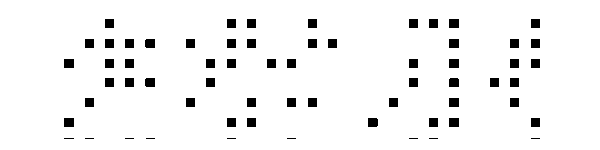

```mathematica
co=Rotate[CO,-1.5708]
```

```mathematica
febf=Overlay[{fe,bf}]
```

-Graphics--Graphics-

```mathematica
MainChart=Overlay[{febf,co}]
```

-Graphics--Graphics--Graphics-

```mathematica
L=BarLegend[{"TemperatureMap",{h,-h}},LegendMarkerSize->600]
```

```mathematica
GraphicsRow[{MainChart,L},ImageSize->Large]
```

-Graphics-